```mathematica
rta[x_,y_,n_]:=If[n==0,Sow[{x,y}],Sow[rta[x,y,n-1]+{3,4}*(-2)^(n-1)]];
```

```mathematica
rpdr[x_,y_,n_]:=Flatten[Reap[rta[x,y,n]][[2]],1];
```

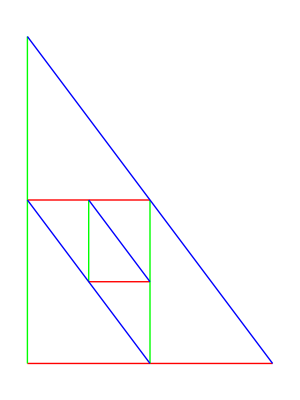

```mathematica
Clear[nt,vtx,xline,yline,hline];nt=3;vtx=rpdr[0,0,nt];xline=Table[{vtx[[i]],{vtx[[i+1]][[1]],vtx[[i]][[2]]}},{i,1,nt}];yline=Table[{vtx[[i]],{vtx[[i]][[1]],vtx[[i+1]][[2]]}},{i,1,nt}];
hline=Table[{{vtx[[i+1]][[1]],vtx[[i]][[2]]},{vtx[[i]][[1]],vtx[[i+1]][[2]]}},{i,1,nt}];
Graphics[{Red,Line[xline],Green,Line[yline],Blue,Line[hline]}]
```